```mathematica
RungeKutta Method 4th
```

```mathematica
$HistoryLength=3;
ClearAll[R,l,Lz,Bz0,Brho,Bz];
Timing[
R=0.08;(*Solenoid radius*)
l=0.3;(*Solenoid length*)
Lz=20;(*Simulation length*)
Bz0=1.7647058823529413;(*Scaling factor of Bz*)
Brho[1]={0.1,0.2,0.5,1.0,3.0,5.0,7.0,9.0,10.0};(*List of rigidity*)
Bz[z_]=((z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2)))/Bz0;(*Scaled Bz field*)

Vari={r};(*Variable of equation*)
Time={z,-Lz/2,0};(*Simulation time*)

DeltaEm1=10^-6;(*Step size of emittance when Brho=0.1~1.0*)
Table[Eqs[i,j]={r''[z]==1/r[z]^3*(DeltaEm1*i)^2-(Bz[z]/(2*Brho[1][[j]]))^2*r[z],r[-Lz/2]==R/2,r'[-Lz/2]==0},{i,1,150},{j,1,4}];(*radial equation*)
Table[SOL[i,j]=NDSolveValue[Eqs[i,j],Vari,Time,Method->{"ExplicitRungeKutta","DifferenceOrder"->4}, MaxSteps->10^5],{i,1,150},{j,1,4}];(*Solve radial equation numerically with 4th order RungeKutta*)


DeltaEm2=10^-7;(*Step size of emittance when Brho=3.0~10*)
Table[Eqs[i,j]={r''[z]==1/r[z]^3*(DeltaEm2*i)^2-(Bz[z]/(2*Brho[1][[j]]))^2*r[z],r[-Lz/2]==R/2,r'[-Lz/2]==0},{i,1,50},{j,5,9,1}];(*radial equation*)
Table[SOL[i,j]=NDSolveValue[Eqs[i,j],Vari,Time,Method->{"ExplicitRungeKutta","DifferenceOrder"->4}, MaxSteps->10^5],{i,1,50},{j,5,9,1}];(*Solve radial equation numerically with 4th order RungeKutta*)
]
```

{3.4926,Null}

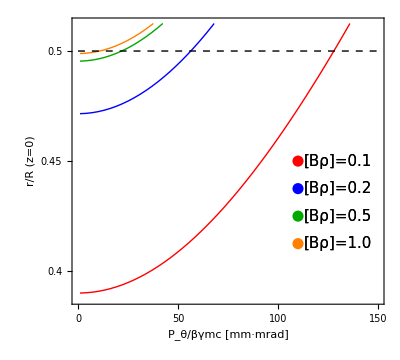

```mathematica
(*Making list of r(z=0) vs P_theta/mgbc and Plot when Brho=0.1~1.0*)

Flatten[Table[LargePtheta[j]=Table[{(DeltaEm1*i)*10^6,SOL[i,j][[1]][0]/R},{i,1,150,3}],{j,1,4}],1];

GList[1]={{{1.3*10^2,0.036/R}},{{1.3*10^2,0.035/R}},{{1.3*10^2,0.034/R}},{{1.3*10^2,0.033/R}}};

PIC[1]=Show[ListPlot[Table[LargePtheta[i],{i,1,4}],PlotRange->{{0,1.5*10^2},{0.031/R,0.041/R}},Joined->True,Frame->True,FrameLabel->{"P_θ/βγmc [mm·mrad]","r/R (z=0)"},LabelStyle->Directive[15],AspectRatio->0.9,PlotStyle->{Red,Blue,Darker[Green],Orange},FrameTicks->{{{{0.032/R,"0.4"},{0.036/R,"0.45"},{0.040/R,"0.5"}},None},{{{0,"0"},{0.5*10^2,"50"},{1*10^2,"100"},{1.5*10^2,"150"}},None}}],

ListPlot[GList[1],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{"[Bρ]=0.1",15},{"[Bρ]=0.2",15},{"[Bρ]=0.5",15},{"[Bρ]=1.0",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListPlot[{{0,0.5},{150,0.5}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Black,Dashed}],

ListPlot[{{1.1*10^2,0.036/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Red,PointSize[0.02]}],
ListPlot[{{1.1*10^2,0.035/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Blue,PointSize[0.02]}],
ListPlot[{{1.1*10^2,0.034/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Darker[Green],PointSize[0.02]}],
ListPlot[{{1.1*10^2,0.033/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Orange,PointSize[0.02]}]]
```

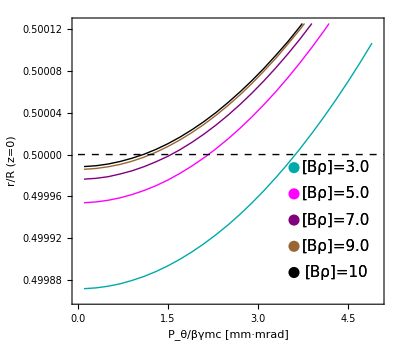

```mathematica
(*Making list of r(z=0) vs P_theta/mgbc and Plot when Brho=3.0~10*)

Flatten[Table[LargePtheta[j]=Table[{(DeltaEm2*i)*10^6,SOL[i,j][[1]][0]/R},{i,1,50,2}],{j,5,9,1}],1];

GList[2]={{{4.3,0.039999/R}},{{4.3,0.039997/R}},{{4.3,0.039995/R}},{{4.3,0.039993/R}},{{4.3,0.039991/R}}};
PIC[2]=Show[ListPlot[Table[LargePtheta[i],{i,5,9,1}],PlotRange->{{0,5},{0.039989/R,0.04001/R}},Joined->True,Frame->True,FrameLabel->{"P_θ/βγmc [mm·mrad]","r/R (z=0)"},LabelStyle->Directive[14],AspectRatio->0.9,PlotStyle->{Darker[Cyan],Magenta,Purple,Brown,Black}],

ListPlot[GList[2],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{"[Bρ]=3.0",15},{"[Bρ]=5.0",15},{"[Bρ]=7.0",15},{"[Bρ]=9.0",15},{"[Bρ]=10",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListPlot[{{0,0.5},{20,0.5}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Black,Dashed}],

ListPlot[{{3.6,0.039999/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Darker[Cyan],PointSize[0.02]}],
ListPlot[{{3.6,0.039997/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Magenta,,PointSize[0.02]}],
ListPlot[{{3.6,0.039995/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Purple,PointSize[0.02]}],
ListPlot[{{3.6,0.039993/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Brown,PointSize[0.02]}],
ListPlot[{{3.6,0.039991/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black,PointSize[0.02]}]]
```

```mathematica
Table[IPLargePtheta[i]=Interpolation[LargePtheta[i]],{i,1,9}];
IPLargePtheta[1][0.00012795];
IPLargePtheta[2][0.0000564];
IPLargePtheta[3][0.0000219];
IPLargePtheta[4][0.0000109];
IPLargePtheta[5][0.0000036];
IPLargePtheta[6][0.0000022];
IPLargePtheta[7][0.0000016];
IPLargePtheta[8][0.0000012];
IPLargePtheta[9][0.0000011];
```

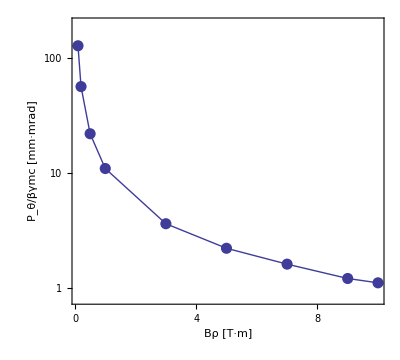

```mathematica
(*Making list of large P_theta vs Brho and Plot*)
Pthe[1]={0.00012795,0.0000564,0.0000219,0.0000109,0.0000036,0.0000022,0.0000016,0.0000012,0.0000011};(*List of large P_theta*)
Brho[1]={0.1,0.2,0.5,1.0,3.0,5.0,7.0,9.0,10.0};
PtheHalf[1]=Table[{Brho[1][[i]],Pthe[1][[i]]*10^6},{i,1,9}];
PIC[3]=Show[ListLogPlot[PtheHalf[1],PlotRange->{All,{0.8,200}},Frame->True,LabelStyle->Directive[15],PlotStyle->{PointSize[0.02]},FrameLabel->{"Bρ [T·m]","P_θ/βγmc [mm·mrad]"},AspectRatio->0.9,FrameTicks->{{{{1,"1"},{10,"10"},{100,"100"}},None},{{{0,"0"},{2,"2"},{4,"4"},{6,"6"},{8,"8"},{10,"10"}},None}}],
ListLogPlot[PtheHalf[1],PlotRange->All,Frame->True,Joined->True]]
```

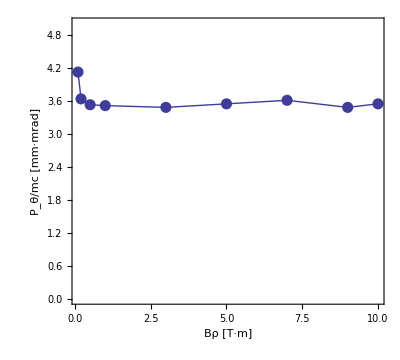

```mathematica
(*Plot of normalized large P_theta*)
BG[1]={0.032184044076469374,0.06436808815293875,0.16092022038234688,0.32184044076469387,0.9655213222940812,1.6092022038234695,2.2528830853528556,2.8965639668822436,3.218404407646942};(*List of beta*gamma for each Brho*)
Brho[1]={0.1,0.2,0.5,1.0,3.0,5.0,7.0,9.0,10.0};

PtheHalf[3]=Table[{Brho[1][[i]],Pthe[1][[i]]*BG[1][[i]]*10^6},{i,1,9}];
PIC[4]=Show[ListPlot[PtheHalf[3],PlotRange->{All,{0,5}},Frame->True,LabelStyle->Directive[17],PlotStyle->{PointSize[0.02]},FrameLabel->{"Bρ [T·m]","P_θ/mc [mm·mrad]"},AspectRatio->0.9],
ListPlot[PtheHalf[3],PlotRange->All,Frame->True,Joined->True]]
```

```mathematica
(*Making list of orbit at large P_theta*)

Timing[
R=0.08;
l=0.3;
Lz=20;
Bz0=1.7647058823529413;
DeltaEm1=10^-6;
DeltaEm2=0.1*10^-6;
Brho[1]={0.1,0.2,0.5,1.0,3.0,5.0,7.0,9.0,10.0};
Pthe[1]={0.00012795,0.0000564,0.0000219,0.0000109,0.0000036,0.0000022,0.0000016,0.0000012,0.0000011};
Bz[z_]=((z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2)))/Bz0;

Vari={r};(*Variable of equation*)
Time={z,-Lz/2,0};(*Simulation time*)
Table[Eqs[i]={r''[z]==1/r[z]^3*(Pthe[1][[i]])^2-(Bz[z]/(2*Brho[1][[i]]))^2*r[z],r[-Lz/2]==R/2,r'[-Lz/2]==0},{i,1,9}];
(*Equation of motion*)

Table[SOL[i]=NDSolveValue[Eqs[i],Vari,Time,Method->{"ExplicitRungeKutta","DifferenceOrder"->4}, MaxSteps->10^5],{i,1,9}];(*Solve equation of motion numerically*)

]
```

{0.04604,Null}

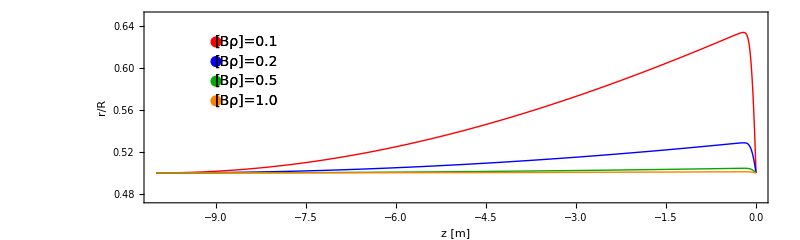

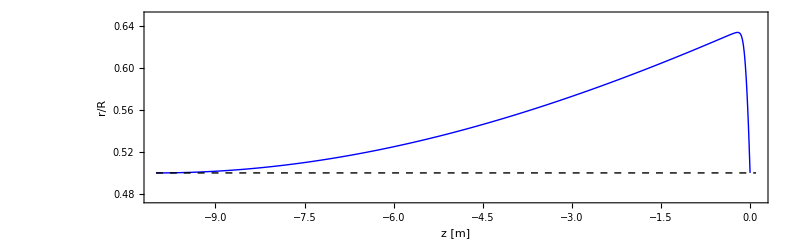

```mathematica
(*Making plot of orbit at large P_theta when Brho=0.1~1.0*)
GList[1]={{{-8.5,0.05/R}},{{-8.5,0.0485/R}},{{-8.5,0.047/R}},{{-8.5,0.0455/R}}};

Table[rz[i]=Table[{z,SOL[i][[1]][z]/R},{z,-Lz/2,0,Lz/2/1000}],{i,1,9}];
RZ[1]=Show[ListPlot[Table[rz[i],{i,1,4}],PlotRange->{{-10,0},{0.038/R,0.052/R}},FrameLabel->{"z [m]","r/R"},AspectRatio->0.3,LabelStyle->Directive[18],Joined->True,Frame->True,PlotStyle->{Red,Blue,Darker[Green],Orange},ImageSize->{800,240}],

ListPlot[GList[1],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{"[Bρ]=0.1",14},{"[Bρ]=0.2",14},{"[Bρ]=0.5",14},{"[Bρ]=1.0",14}},BaseStyle->{FontFamily->"Times",FontSize->18}],

ListPlot[{{-9,0.05/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Red,PointSize[0.01]}],
ListPlot[{{-9,0.0485/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Blue,PointSize[0.01]}],
ListPlot[{{-9,0.047/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Darker[Green],PointSize[0.01]}],
ListPlot[{{-9,0.0455/R}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Orange,PointSize[0.01]}]]

(*Sample orbit at large P_theta when Brho=0.1*)
Orb[1]=Show[ListPlot[Table[rz[i],{i,1}],PlotRange->{{-10,0.1},{0.038/R,0.052/R}},FrameLabel->{"z [m]","r/R"},AspectRatio->0.3,LabelStyle->Directive[18],Joined->True,Frame->True,PlotStyle->{Blue,Darker[Green],Orange},ImageSize->{800,240}],
ListPlot[{{-10,0.5},{0.1,0.5}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Black,Dashed}]
]
```

```mathematica
(*Export graphic data to the directory on your computer:you have to specify the directory where you want to export*)

Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Valid_Ptheta1.eps",PIC[1],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Valid_Ptheta2.eps",PIC[2],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Valid_UnEmit.eps",PIC[3],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Valid_NormEmit_Proton.eps",PIC[4],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Valid_NormEmit_RZ_Orb.eps",RZ[1],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Valid_NormEmit_sample_Orb.eps",Orb[1],"EPS"];
```